# Particle Diffusion

Michael Jones and Ian Jackson

```mathematica
Clear["`*"]
Needs["Units`"]
```

2D draw path function

```mathematica
drawPath2D[{a_,num_,c_,l_,w_}]:=Module[{R,σ,width,height,objectX,objectY,V,λ,collisions,pathLength,pathAngle,coordinates,index,newX,newY,min,max,distance},
R=ElementData[a,"AtomicRadius"]/LinguisticAssistant; (* Import atom data *)
σ=Pi R^2; (* Atom's cross section *)
width=w;
height=l;
objectX=width/2; (* Starting Position *)
objectY=height/2;
V=width height (2 R); (* Container Volume *)
n=num/V; (* Particle Density *)
λ=1/(n σ); (* Mean Free Path *)
collisions=c;
pathLength={}; (* Create an array of size collisions with somewhat varied path lengths, keeping them mostly closer to λ *)
Do[pathLength=Append[pathLength,λ+λ (-1)^RandomInteger[1] (E^(-RandomReal[{.25,4}]))],collisions];
pathAngle=RandomReal[2 Pi,collisions]; (* Creates an array of path angles *)
coordinates={{objectX,objectY}};
min=objectX;
max=objectX;
index=1;
Do[newX=coordinates[[index,1]]+pathLength[[index]] Cos[pathAngle[[index]]]; (* Find all coordinates along the path *)
newY=coordinates[[index,2]]+pathLength[[index]] Sin[pathAngle[[index]]];
coordinates=Append[coordinates,{newX,newY}];
If[newX<min,min=newX];
If[newY<min,min=newY];
If[newX>max,max=newX];
If[newY>max,max=newY];
index++;,
collisions];
distance=EuclideanDistance[coordinates[[1]],coordinates[[collisions+1]]]; (* Calculate total distance traveled *)
{Graphics[{Black,Line[coordinates],Red,Line[{coordinates[[1]],coordinates[[collisions+1]]}],Blue,Opacity[.1],Rectangle[{0,0},{width,height}]},Frame->True,PlotRange->{{min,max},{min,max}},ImageSize->Medium],distance} (* Plot the path and return the distance *)
]
```

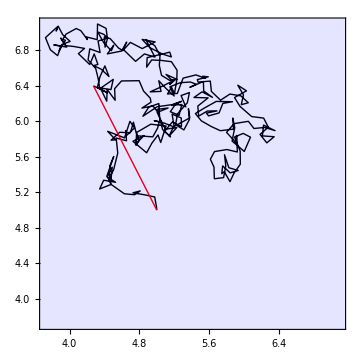

1.57691

```mathematica
{plot,distance}=drawPath2D[{"Hydrogen",10000000,300,10,10}]; (* Test the function above *)
plot
distance
```

3D draw path function

```mathematica
drawPath3D[{a_,num_,c_,l_,w_,d_}]:=Module[{R,σ,width,height,depth,objectX,objectY,objectZ,V,λ,collisions,pathLength,pathAngle,pathAngleVert,coordinates,index,newX,newY,newZ,min,max,distance},
R=ElementData[a,"AtomicRadius"]/LinguisticAssistant; (* Import atom data *)
σ=Pi R^2; (* Atom Cross Section *)
width=w;
height=l;
depth=d;
objectX=width/2; (* Starting Coordinates *)
objectY=height/2;
objectZ=depth/2;
V=width height depth; (* Container Volume *)
n=num/V; (* Density of Particles in Volume *)
λ=1/(n σ); (* Mean Free Path *)
collisions=c;
pathLength={}; (* Create array of path lengths, varying slightly *)
Do[pathLength=Append[pathLength,λ+λ (-1)^RandomInteger[1] (E^(-RandomReal[{.25,4}]))],collisions];
pathAngle=RandomReal[2 Pi,collisions]; (* Create array of x-y angles *)
pathAngleVert=RandomReal[{-Pi/2,Pi/2},collisions]; (* Create array of z angle *)
coordinates={{objectX,objectY,objectZ}};
min=objectX;
max=objectX;
index=1; (* Find all coordinates *)
Do[newX=coordinates[[index,1]]+pathLength[[index]] Cos[pathAngleVert[[index]]] Cos[pathAngle[[index]]]; 
newY=coordinates[[index,2]]+pathLength[[index]] Cos[pathAngleVert[[index]]] Sin[pathAngle[[index]]];
newZ=coordinates[[index,3]]+pathLength[[index]] Sin[pathAngleVert[[index]]];
coordinates=Append[coordinates,{newX,newY,newZ}];
If[newX<min,min=newX];
If[newY<min,min=newY];
If[newZ<min,min=newZ];
If[newX>max,max=newX];
If[newY>max,max=newY];
If[newZ>max,max=newZ];
index++;,
collisions];
distance=EuclideanDistance[coordinates[[1]],coordinates[[collisions+1]]]; (* Find total distance traveled *)
{Graphics3D[{Black,Line[coordinates],Red,Line[{coordinates[[1]],coordinates[[collisions+1]]}],Blue,Opacity[0.1],Cuboid[{0,0,0},{width,height,depth}]},PlotRange->{{min,max},{min,max},{min,max}},Axes->True,ImageSize->Medium],distance} (* Plot the path and return the distance *)
]
```

```mathematica
{plot,distance}=drawPath3D[{"Hydrogen",1000000000000,1000,10,10,10}]; (* Test the above function *)
plot
distance
```

-Graphics3D-

2.2828

```mathematica
(* Function to calculate the theoretical distance traveled based on the same parameters (3D travel) *)
calculateDrms3D[{a_,num_,c_,l_,w_,d_}]:=Module[{R,V,n,σ,λ},
R=ElementData[a,"AtomicRadius"]/LinguisticAssistant;
V=l w d;
n=num/V;
σ=Pi R^2;
λ=1/(n σ);
Sqrt[c] λ
]
```

```mathematica
calculateDrms3D[{"Hydrogen",1000000000000,1000,10,10,10}]
```

4.

```mathematica
(* Function to calculate the theoretical distance traveled based on the same parameters (2D travel) *)
calculateDrms2D[{a_,num_,c_,l_,w_}]:=Module[{R,V,n,σ,λ},
R=ElementData[a,"AtomicRadius"]/LinguisticAssistant;
V=l w 2 R;
n=num/V;
σ=Pi R^2;
λ=1/(n σ);
Sqrt[c] λ
]
```

```mathematica
calculateDrms2D[{"Hydrogen",10000000,300,10,10}]
```

2.

```mathematica
meanTrials[{a_,num_,c_,l_,w_,d_},trials_]:=Module[{sum},
sum=0;
Do[sum=sum+drawPath3D[{a,num,c,l,w,d}][[2]],trials];
sum/trials
]
meanTrials[{"Hydrogen",1000000000000,1000,10,10,10},1000]
```

3.51703

```mathematica
DynamicModule[{output=""},
Panel[
Column[{
Button["Do",output="Paused...";
Pause[3];
output="Done.";,
Method->"Queued"],
Panel[Pane[Dynamic[output,TrackedSymbols:>{output}],{100,50}]]
}]
]
]
```